```mathematica
(** Various helper functions for standard parts of the paper / reachable set results **)
CW[n_] := {{0, 0, 0,1, 0, 0}, {0, 0, 0,0,1, 0}, {0, 0, 0, 0 ,0, 1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0, 0}, {0, 0, -n^2, 0, 0,0}} ;
cmat[ab_, tau_, tf_] := MatrixExp[-(tau - tf) ab // Transpose][[4;;6, 1;;3]];
xrf[tf_, delta_, h_, deltaT_, A_, n_, Rr_, emax_] := NIntegrate[  emax (cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta / (deltaT.(cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta // Sqrt)[[1]]  ,{tau, 0, tf}];
x3fanalytical[tf_, h_, n_]:= h(2Floor[n tf / Pi]+1+ Mod[Floor[n tf / Pi], 2] Cos[n tf] - (Mod[Floor[n tf / Pi], 2] - 1)(- Cos[n tf]));
```

```mathematica
(** Computes the thrust-limited reachable set for a given final time **)
thrustreachable[xrf_,tf_, na_, emax_] := Module[{points, tfs, hs, As, ns, Rrs, pointsT, rd, rdpoints, rdboundary, first2},
points = CirclePoints[1000];
points = Append[#, 0] & /@ points;
points //  N;
points[[1]];
tfs = ConstantArray[tf, 1000];
tfs[[1]];
hs = ConstantArray[1, 1000];
hs[[1]];
As = ConstantArray[CW[na], 1000];
As[[1]] // MatrixForm;
ns = ConstantArray[na, 1000];
ns[[1]];
Rrs = ConstantArray[1, 1000];
Rrs[[1]];
emaxs = ConstantArray[emax, 1000];
columntorow[x_] := {x};
pointsT = columntorow /@ points;
pointsT[[1]] // MatrixForm;
rd = MapThread[xrf, {tfs, points, hs, pointsT, As, ns, Rrs, emaxs}];
rdpoints = Map[Re, rd, {2}];
rdboundary = PolygonCoordinates[ConvexHullRegion[rdpoints]];
first2[x_] := {x[[1]], x[[2]]};
(* rboundary = Map[first2, rdboundary];*)
rdboundary
]
```

```mathematica
(** Computes the energy reachable quadratic form for an associated n and final time **)
energyform[tff_, na_] := Module[{c, r, sig, gamma, nmat},
c[n_] = {
{0, -2* n, 0, 1, 0, 0},
{2 * n, 0, 0, 0, 1, 0},
{0, 0, 0, 0,0 , 1},
{-1, 0, 0, 0, 0, 0},
{0, -1, 0, 0,0,0 }, 
{0, 0, -1, 0, 0, 0 }
}; (*Good*)
c[n] // MatrixForm;
r[t_, n_] = {{72  * t  * Cos[n * t] + (154 * n * t + 48 * n ^ 3 * t ^ 3 - 384 * Sin[n * t] - 27 * Sin[2 * n * t]) / (4 * n), -3 * n * t ^ 2 + (6 - 6 * Cos[n * t] ) / n, 0, (8+12 * n^2* t^2−8* Cos[n * t]−24*n* t* Sin[n * t]+9 *Sin[ n * t]^2 )/ (2 * n ^ 2), (23 *n * t+6 *n^3 *t^3+42*n*t* Cos[ n * t]−56 * Sin[ n * t]−(9/2) * Sin [2*n*t])/n^2, 0
},
{-3 * n * t ^ 2 + (6 - 6 * Cos[n * t] ) / n, t, 0,  (-2*n * t + 2 * Sin[n * t]) / n^2, - 3 * t^2 / 2 + (4 - 4 Cos[n * t])/n ^ 2, 0 
},
{
0, 0, ( 2 * n * t + Sin[2 * n * t]) / (4 *n) , 0, 0, Sin[n * t] ^ 2 / (2 * n^2)
},
{(8+12 * n^2* t^2−8* Cos[n * t]−24*n* t* Sin[n * t]+9 *Sin[ n * t]^2 )/ (2 * n ^ 2), (-2*n * t + 2 * Sin[n * t]) / n^2, 0, (26 * n * t - 32 * Sin[n * t] + 3 * Sin[2 * n * t]) / (4 * n^3), 3 * (- n * t + Sin[n * t])^2/ n ^ 3, 0
},
{(23 *n * t+6 *n^3 *t^3+42*n*t* Cos[ n * t]−56 * Sin[ n * t]−(9/2) * Sin [2*n*t])/n^2, - 3 * t^2 / 2 + (4 - 4 Cos[n * t])/n ^ 2, 0, 3* (-n *t + Sin[n * t])^2 / n^3,(14 * n * t + 3 * n^3 * t^3 + 24 * n * t * Cos[n * t] - 32 * Sin[n * t] - 3 * Sin[ 2 *n *t]) / n ^3 , 0 
}, 
{0, 0,  Sin[n * t] ^ 2 / (2 * n^2), 0, 0, (2 * n * t - Sin[2 * n *t ]) / (4 * n^3)
}
};(*Good*)
r[t, n] // MatrixForm;
sig[t_, n_] = {{4-3 Cos[n t],0,0,Sin[n t]/n,(2-2 Cos[n t])/n,0},{6 (-n t+Sin[n t]),1,0,(2 (-1+Cos[n t]))/n,-3 t+(4 Sin[n t])/n,0},{0,0,Cos[n t],0,0,Sin[n t]/n},{3 n Sin[n t],0,0,Cos[n t],2 Sin[n t],0},{6 n (-1+Cos[n t]),0,0,-2 Sin[n t],-3+4 Cos[n t],0},{0,0,-n Sin[n t],0,0,Cos[n t]}}; (* Good *)
gamma[t_, t0_, n_] = sig[t, n]. (sig[t0, n] // Inverse);

nmat[t0_, tf_, n_] = (Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2] // Transpose). (c[n] // Transpose). (r[tf, n] // Inverse).c[n].Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2];
nmat[0, tff, na]
]
mu1 = 3.986 10^14 ;
endTime = 1500;
alpha = 7780000;
n = (mu1 / alpha^3)^(1/2);
tmax=2/1000;
comparableenergy = endTime tmax^2
(** 
testbounds = thrustreachable[xrf, endTime, n, tmax];
testbounds // MatrixForm; **)

(* tmax = h n^2 Rr, i have h = 100, Rr = 1. So the energy associated to thrust reachable set for comparison is equal to tf ( = 1600) * h n^2*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
reachablestatsoperator[b_, points_, em_] := Module[{rats, vecs}, 

ratio[pos_, quad_]:= ((em *(Eigenvalues[{Join[Join[({pos // Normalize} // Transpose).{pos // Normalize}, {{0,0,0}, {0,0,0}, {0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}])[[1]]) // Sqrt) / Norm[pos];
maxminrat[a_, v1s_] := {MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Max,   MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Min };
maxminvec[a_, v1s_] := {v1s[[  Position[MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}], MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Max    ][[1, 1]] ]], v1s[[  Position[MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}], MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Min    ][[2, 1]] ]]};
rats = maxminrat[b, points];
vecs = maxminvec[b, points];
{rats , vecs}
]
```

```mathematica
(** Threading the different terminal times through our energy and thrust limited RRS computations, and then through the ratio computations **) 
starts // Clear;
finaltime // Clear;
starts = 1500; 
finaltime = 1700;


terminaltimes = Range[starts, finaltime, 50];
ns = ConstantArray[n, terminaltimes // Length];
tmaxs = ConstantArray[tmax, terminaltimes // Length];
xrfs = ConstantArray[xrf, terminaltimes // Length];
bounds = MapThread[thrustreachable, {xrfs, terminaltimes, ns, tmaxs}];
forms = MapThread[energyform, {terminaltimes, ns}];
comparableenergies = terminaltimes tmax^2;
computedmmratios = MapThread[reachablestatsoperator, {forms, bounds, comparableenergies} ]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{{1.30008,1.12657},{{778.607,-2291.24,0.},{1081.55,1659.81,0.}}},{{1.3153,1.12518},{{763.839,-2463.74,0.},{1158.77,1752.69,0.}}},{{1.33148,1.12374},{{760.898,-2642.74,0.},{1266.87,1828.14,0.}}},{{1.3486,1.12234},{{749.992,-2826.54,0.},{1381.66,1900.96,0.}}},{{1.36667,1.12099},{{729.857,-3014.35,0.},{1467.94,1996.38,0.}}}}

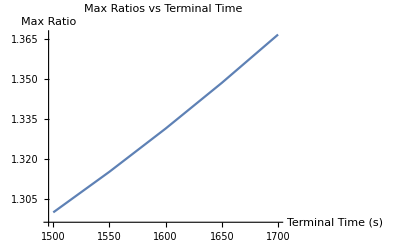

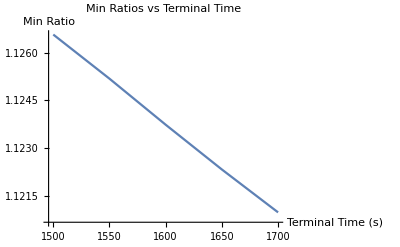

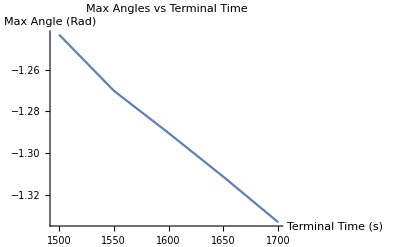

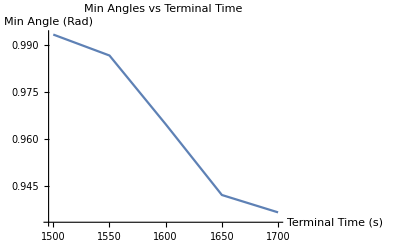

```mathematica
maxrats = computedmmratios[[;;, 1, 1]];
minrats = computedmmratios[[;;, 1, 2]];
maxvecs = computedmmratios[[;;, 2, 1]];
minvecs = computedmmratios[[;;, 2, 2]];
vectoangle[k_] := ArcTan[k[[1]],k[[2]]];

maxangles = Map[vectoangle, maxvecs];
minangles = Map[vectoangle, minvecs];

ListLinePlot[{terminaltimes, maxrats} // Transpose, PlotLabel -> "Max Ratios vs Terminal Time", AxesLabel-> {"Terminal Time (s)", "Max Ratio" }   ]
ListLinePlot[{terminaltimes, minrats} // Transpose, PlotLabel-> "Min Ratios vs Terminal Time", AxesLabel-> {"Terminal Time (s)", "Min Ratio" }]
ListLinePlot[{terminaltimes, maxangles} // Transpose, PlotLabel -> "Max Angles vs Terminal Time", AxesLabel-> {"Terminal Time (s)", "Max Angle (Rad)" }]
ListLinePlot[{terminaltimes, minangles} // Transpose, PlotLabel->"Min Angles vs Terminal Time", AxesLabel-> {"Terminal Time (s)", "Min Angle (Rad)"}]
```

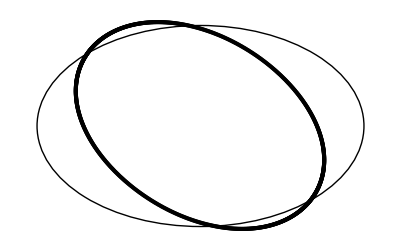

```mathematica
energyseteigenvalues[quad_] :=  Eigenvalues[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}]

energysetaxes[quad_] :=
Eigenvectors[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}]

vecs = energysetaxes[energyform[endTime, n]];
vals = energyseteigenvalues[energyform[endTime, n]];
ax1 = vecs[[1]][[1;;2]] * ((comparableenergy * vals[[1]]) // Sqrt);
ax2 = vecs[[2]][[1;;2]] * ((comparableenergy * vals[[2]]) // Sqrt);

{ax1, ax2} // Transpose// MatrixForm;

ax1length = Norm[ax1];
ax2length = Norm[ax2];
testbounds // Dimensions;
testbounds[[;;, 1;;2]] // Point;
Show[Graphics[GeometricTransformation[Circle[{0,0}, {ax1length, ax2length }], RotationTransform[ax1 // vectoangle]]], Graphics[Point[testbounds[[;;, 1 ;; 2]]]]]



(**
Show[{Graphics[Point[bounds]], Graphics[Circle[{0, 0}, {100, 1000}]], Graphics[Line[5000 AnglePath[{stats[[1]] // vectoangle}]]], Graphics[Line[5000AnglePath[{stats[[2]] // vectoangle}]]]}]  **)
```